```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergies,SelfEnergyCTs}];
```

## u u → t t (1-loop)

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 2 Particles insertions

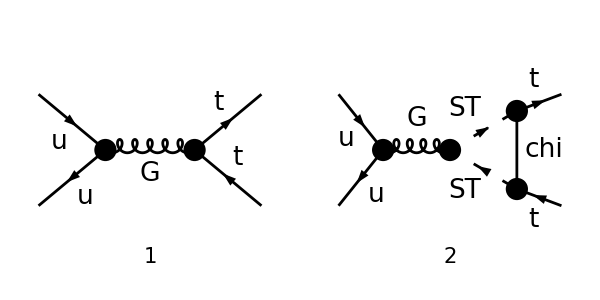

```mathematica
tops0 = CreateTopologies[0,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
tops = CreateTopologies[1,2->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles,SelfEnergies}];
processGGT =  { F[7],-F[7]} -> {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8],F[9]}];
goodDiags=allDiags;
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->False]/.{SUNT->FASUNT},IncomingMomenta->{k1,k2},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,DropSumOver->True,SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs};
ampB =FullSimplify[SUNSimplify[DiracSimplify[ampA]]]
```

in total: 2 Particles amplitudes

-1/(p1+p2)^2 gs^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((yDM^2 ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))+2 (φ(-k2)).(γ·q).(φ(k1))) (φ(p1,MT)).(γ·q).(γ̄)^6.(φ(-p2,MT)))/(q^2-mChi^2).((p1+q)^2-mST^2).((p2-q)^2-mST^2)+ⅈ (φ(-k2)).γ^Lor2.(φ(k1)) ((2 π^2 deltaCTL yDM^2+1) (φ(p1,MT)).γ^Lor2.(γ̄)^7.(φ(-p2,MT))+(2 π^2 deltaCTR yDM^2+1) (φ(p1,MT)).γ^Lor2.(γ̄)^6.(φ(-p2,MT))))

```mathematica
ampC =( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->True,ToPaVe->True]//Simplify)/.{LorentzIndex[a_,D]->LorentzIndex[μ,D]}
```

-1/(p1+p2)^2 ⅈ gs^2 (π^2 ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)) C_1(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mChi^2,mST^2,mST^2) yDM^2-π^2 ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)) C_2(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mChi^2,mST^2,mST^2) yDM^2+2 π^2 (φ(-k2)).γ^μ.(φ(k1)) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) C_00(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mChi^2,mST^2,mST^2) yDM^2+2 π^2 (φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT)) C_11(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mChi^2,mST^2,mST^2) yDM^2-2 π^2 ((φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p1).(γ̄)^6.(φ(-p2,MT))+(φ(-k2)).(γ·p1).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT))) C_12(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mChi^2,mST^2,mST^2) yDM^2+2 π^2 (φ(-k2)).(γ·p2).(φ(k1)) (φ(p1,MT)).(γ·p2).(γ̄)^6.(φ(-p2,MT)) C_22(p1^2,p1^2+2 (p1·p2)+p2^2,p2^2,mChi^2,mST^2,mST^2) yDM^2+(φ(-k2)).γ^μ.(φ(k1)) (2 deltaCTR π^2 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) yDM^2+2 deltaCTL π^2 (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)) yDM^2+(φ(p1,MT)).γ^μ.((γ̄)^6+(γ̄)^7).(φ(-p2,MT)))) T_Col2Col1^Glu5 T_Col3Col4^Glu5

```mathematica
(* Remove SM contribution *)
ampSM=gs^2 SeriesCoefficient[ampC,{gs,0,2},{yDM,0,0}];
ampC=Simplify[ampC-ampSM];
```

## On - Shell Case :

```mathematica
FCClearScalarProducts[];
ScalarProduct[p1,p1]=MT^2;
ScalarProduct[p2,p2]=MT^2;
ScalarProduct[p1,p2]=s/2-MT^2;
```

```mathematica
ampE = Expand[Collect[Simplify[(  ampC)/.aS->GS^2/(4 Pi),Assumptions->{GS>0}],{Pair[LorentzIndex[μ,D],Momentum[p1,D]],Pair[LorentzIndex[μ,D],Momentum[p2,D]],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[6],DiracGamma[LorentzIndex[μ,D],D].DiracGamma[7]},FullSimplify]];
```

```mathematica
ampEsimp=FullSimplify[DiracSimplify[ampE//.{PaVe[0,0,a_,b_,c_,d_]->C00,PaVe[1,1,a_,b_,c_,d_]->C11,PaVe[1,2,a_,b_,c_,d_]->C12,PaVe[1,a_,b_,c_,d_]->C1}]]
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 (φ(-k2)).γ^μ.(φ(k1)) ((C00+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+deltaCTL (φ(p1,MT)).γ^μ.(γ̄)^7.(φ(-p2,MT)))-MT (φ(-k2)).(γ·p2).(φ(k1)) ((C1+2 C11) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))+(C1+2 C12) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT)))+MT (φ(-k2)).(γ·p1).(φ(k1)) ((C1+2 C11) (φ(p1,MT)).(γ̄)^6.(φ(-p2,MT))+(C1+2 C12) (φ(p1,MT)).(γ̄)^7.(φ(-p2,MT))))

```mathematica
ampEsimp2=FullSimplify[DotSimplify[DiracSimplify[ampEsimp,DiracSubstitute67->True]]]
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((C00-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(C00+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+MT (C11-C12) (φ(p1,MT)).(γ̄)^5.(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))+(φ(-k2)).(γ·p2).(φ(k1)))+MT (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
sps=Cases2[ampEsimp2,Spinor]
moms=Cases2[ampEsimp2,DiracGamma]
```

{φ(k1),φ(-k2),φ(p1,MT),φ(-p2,MT)}

{(γ̄)^5,γ^μ,γ·p1,γ·p2}

```mathematica
(* phi(k1).p1slash.phi(-k2) + phi(k1).p2slash.phi(-k2) = phi(k1).(p1slash+p2slash).phi(-k2) = phi(k1).(k1slash+k2slash).phi(-k2) = 0 *)
ampEsimp3=Collect[ampEsimp2,{sps[[3]].moms[[1]].sps[[4]]},Simplify]/.{sps[[2]].moms[[3]].sps[[1]]+sps[[2]].moms[[4]].sps[[1]]->0}
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 ((φ(-k2)).γ^μ.(φ(k1)) ((C00-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^5.(φ(-p2,MT))+(C00+deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+MT (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
ampEsimp4=FullSimplify[DiracSimplify[DiracSimplify[ampEsimp3,DiracSubstitute5->True]/.(DiracGamma[7]->1-DiracGamma[6])]]
```

-1/(p1+p2)^2 ⅈ π^2 gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (2 (φ(-k2)).γ^μ.(φ(k1)) ((C00-deltaCTL+deltaCTR) (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT))+deltaCTL (φ(p1,MT)).γ^μ.(φ(-p2,MT)))+MT (C1+C11+C12) (φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1))-(φ(-k2)).(γ·p2).(φ(k1))))

```mathematica
ampF=Collect[ampEsimp4,{sps[[2]].moms[[2]].sps[[1]],sps[[3]].moms[[2]].DiracGamma[6].sps[[4]],sps[[3]].moms[[2]].sps[[4]],sps[[2]].moms[[3]].sps[[1]],sps[[2]].moms[[4]].sps[[1]]},FullSimplify]
```

(φ(-k2)).γ^μ.(φ(k1)) (-1/(p1+p2)^2 2 ⅈ π^2 deltaCTL gs^2 yDM^2 T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(φ(-p2,MT))-1/(p1+p2)^2 2 ⅈ π^2 gs^2 yDM^2 (C00-deltaCTL+deltaCTR) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)))+-1/(p1+p2)^2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p1).(φ(k1))+1/(p1+p2)^2 ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12) T_Col2Col1^Glu5 T_Col3Col4^Glu5 (φ(p1,MT)).(φ(-p2,MT)) (φ(-k2)).(γ·p2).(φ(k1))

### Coefficients for each term

```mathematica
factor=FeynAmpDenominator[PropagatorDenominator[Momentum[p1,D]+Momentum[p2,D],0]]SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col2],SUNFIndex[Col1]]*SUNTF[{SUNIndex[Glu5]},SUNFIndex[Col3],SUNFIndex[Col4]];
CVV = Coefficient[ ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]]]
CVR=Coefficient[ampF,factor sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]]]
CP1=Coefficient[ampF,factor sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]]]
CP2=Coefficient[ampF,factor sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]]]
Coeffs={CVV,CVR,CP1,CP2};
```

-2 ⅈ π^2 deltaCTL gs^2 yDM^2

-2 ⅈ π^2 gs^2 yDM^2 (C00-deltaCTL+deltaCTR)

-ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12)

ⅈ π^2 gs^2 MT yDM^2 (C1+C11+C12)

## EFT Limit

```mathematica
SubsPV={C00->PaXEvaluate[ PaVe[0,0,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C11->PaXEvaluate[ PaVe[1,1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C12-> PaXEvaluate[PaVe[1,2,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))},C1->PaXEvaluate[ PaVe[1,{MT^2,s,MT^2},{mChi^2,mST^2,mST^2}],PaXImplicitPrefactor->1/(2 Pi)^(4-2 Epsilon),PaXSeries->{{MT,0,2},{s,0,1}}]/.{EulerGamma->0,ScaleMu->mST/(√(4 Pi))}};
SubsCT={deltaCTL-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((2*Sqrt[lA]*(xT*(-2+2 xC+xT)+(-(-1+xC)^2+xT)*Log[xC])-4*(-(-1+xC)^3+(-2+xC+xC^2) xT+xT^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),deltaCTR-> (1/(128*xT^2*Sqrt[lA]*Pi^4))*((-1+xC-xT)*(Sqrt[lA]*(2*xT-(-1+xC+xT)*Log[xC])+2*((-2+xC)*xC+(-1+xT)^2)*Log[(1+xC+Sqrt[lA]-xT)/(2*Sqrt[xC])])),xC-> mChi^2/mST^2,xT-> MT^2/mST^2,lA-> (1+xC^2+xT^2-2*xC-2*xT-2*xT*xC)};
```

```mathematica
CoeffsEFTa=Table[Normal[Series[Coeffs[[i]]/.SubsPV//.SubsCT/.{MT->x MT,s-> x^2 s},{x,0,2}]]/.{x->1},{i,1,Length[Coeffs]}];
```

```mathematica
CoeffsEFTb=Table[Assuming[{mST>0,mChi>0,mST>mChi,MT>0,mST>MT+mChi},Collect[CoeffsEFTa[[i]],{Epsilon,MT,s},FullSimplify]],{i,1,Length[CoeffsEFTa]}];
```

```mathematica
Print["CVV=",CoeffsEFTb[[1]]]
```

CVV=(ⅈ gs^2 MT^2 yDM^2 (2 mChi^6+3 mST^2 mChi^4+12 mST^2 log(mST/mChi) mChi^4-6 mST^4 mChi^2+mST^6))/(96 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["CVR=",CoeffsEFTb[[2]]]
```

CVR=-(ⅈ gs^2 s (12 log(mChi/mST) mChi^6-11 mChi^6+18 mST^2 mChi^4-9 mST^4 mChi^2+2 mST^6) yDM^2)/(576 (mChi^2-mST^2)^4 π^2)-(ⅈ gs^2 yDM^2)/(32 ε π^2)

```mathematica
Print["CP1=",CoeffsEFTb[[3]]]
```

CP1=-(ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["CP2=",CoeffsEFTb[[4]]]
```

CP2=(ⅈ gs^2 MT yDM^2 (2 mChi^6+3 mST^2 mChi^4-12 mST^2 log(mChi/mST) mChi^4-6 mST^4 mChi^2+mST^6))/(192 (mChi^2-mST^2)^4 π^2)

```mathematica
Print["amp=",Simplify[factor (sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].sps[[4]] Subscript[C, VV] + sps[[2]].moms[[2]].sps[[1]] sps[[3]].moms[[2]].DiracGamma[6].sps[[4]] Subscript[C, VR] + sps[[2]].moms[[3]].sps[[1]] sps[[3]].sps[[4]] Subscript[C, P1] +sps[[2]].moms[[4]].sps[[1]] sps[[3]].sps[[4]] Subscript[C, P2])]]
```

amp=1/(p1+p2)^2((φ(p1,MT)).(φ(-p2,MT)) ((φ(-k2)).(γ·p1).(φ(k1)) C_P1+(φ(-k2)).(γ·p2).(φ(k1)) C_P2)+(φ(-k2)).γ^μ.(φ(k1)) ((φ(p1,MT)).γ^μ.(γ̄)^6.(φ(-p2,MT)) C_VR+(φ(p1,MT)).γ^μ.(φ(-p2,MT)) C_VV)) T_Col2Col1^Glu5 T_Col3Col4^Glu5